```mathematica
MacArthur - Rosenzweig Paradox of Enrichment model
```

```mathematica
Clear["Global`*"]
dRdt=b R (1-α R) - (a R C)/(1 + a h R)
dCdt= (e a R C)/(1 + a h R) - d C
```

-(a C R)/(1+a h R)+b R (1-R α)

-C d+(a C e R)/(1+a h R)

```mathematica
(* Solve for isoclines *)
Rstar=Solve[dCdt==0,R]
Cstar=Solve[dRdt==0,C]
```

{{R→d/(a (e-d h))}}

{{C→-(b (1+a h R) (-1+R α))/a}}

```mathematica
(* Solve for equilibria *)
equil=Solve[{dRdt==0,dCdt==0},{R,C}];
%//TableForm
```

R→0 | C→0
R→d/(a (e-d h)) | C→(a b e^2-a b d e h-b d e α)/(a^2 (e-d h)^2)
R→1/α | C→0

```mathematica
parms={b-> 0.8,α-> 0.1,a-> 0.25,e-> 0.1,h-> 1.5, d-> 0.05};
```

```mathematica
equil/.parms//TableForm
```

R→0 | C→0
R→8. | C→2.56
R→10. | C→0

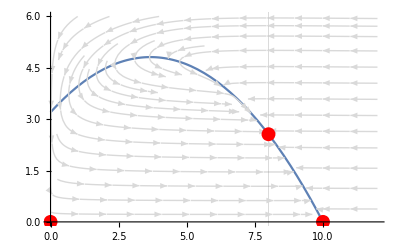

```mathematica
Plot1=Plot[Cstar[[1,1,2]]/.parms,{R,0,12},GridLines->{{{Rstar[[1,1,2]]/.parms,{Red,Thick}}},None},PlotRange->{All,{0,6}} ];Plot2=StreamPlot[{dRdt,dCdt}/.parms,{R,0,12},{C,0,6},StreamStyle->LightGray];
Show[Plot1,Plot2,Graphics[{PointSize[0.025],Red,Point[equil[[All,All,2]]/.parms]}]]
```

```mathematica
Type III functional response
```

```mathematica
Clear["Global`*"]
dRdt=b R (1-α R) - (a R^m C)/(1 + a h R^m)
dCdt= (e a R^m C)/(1 + a h R^m) - d C
```

-(a C R^m)/(1+a h R^m)+b R (1-R α)

-C d+(a C e R^m)/(1+a h R^m)

```mathematica
(* Solve for isoclines  & Solve for equilibria *)
Rstar=Solve[dCdt==0,R]
Cstar=Solve[dRdt==0,C]

equil=Solve[{dRdt==0,dCdt==0},{R,C}];
%//TableForm
```

{{R→(-(-a e+a d h)/d)^(-1/m)}}

{{C→-(b R^(1-m) (1+a h R^m) (-1+R α))/a}}

Solve[{-(a C R^m)/(1+a h R^m)+b R (1-R α)==0,-C d+(a C e R^m)/(1+a h R^m)==0},{R,C}]

```mathematica
Note error messages!  This is because the Hill Exponent m affects the curviness of the equation (i.e. the functional response).  Without m being specified, there may be no prey dependence at all (m = 0), the curviness could be absent (m = 1 -> Type II functional response), or it could be any kind of crazy curviness (m >> 1) that introduces a potentially infinite number of solutions.  Thus Mathematica has no way of solving the equations! 
The resolution is to specify a value for m.  Say m = 2.
```

a any be could crazy curviness has infinite introduces it kind Mathematica no Null number of^3 or potentially solving that the way solutions.Thus equations!

2.

```mathematica
(* Type III functional response, with m=2 *)
(* Solve for isoclines  & Solve for equilibria *)
Rstar=Solve[(dCdt/.{m-> 2})==0,R]
Cstar=Solve[(dRdt/.{m-> 2})==0,C]

equil=Solve[{(dRdt/.{m-> 2})==0,(dCdt/.{m-> 2})==0},{R,C}];
%//TableForm
```

{{R→-(√d)/(√(a e-a d h))},{R→(√d)/(√(a e-a d h))}}

{{C→-(b (1+a h R^2) (-1+R α))/(a R)}}

R→0 | C→0
R→-(√d)/(√(a e-a d h)) | C→((a b √d e^2)/(√(a (e-d h)))-(a b d^(3/2) e h)/(√(a (e-d h)))+b d e α)/(-a d e+a d^2 h)
R→(√d)/(√(a e-a d h)) | C→(-(a b √d e^2)/(√(a (e-d h)))+(a b d^(3/2) e h)/(√(a (e-d h)))+b d e α)/(-a d e+a d^2 h)
R→1/α | C→0

```mathematica
Note that we now have 2 potential R* isoclines and thus 2 coexistence equilibria.  Nevertheless, as you'll see if you plug in parameter values and/or you might be able to reason out for yourself, only one will be in the positive (i.e. "feasible") quadrant.
```

```mathematica
parms={b-> 0.8,α-> 0.1,a-> 0.25,e-> 0.1,h-> 1.5, d-> 0.05,m->2};
```

```mathematica
equil/.parms//TableForm
```

R→0 | C→0
R→-2.82843 | C→-5.80548
R→2.82843 | C→3.24548
R→10. | C→0

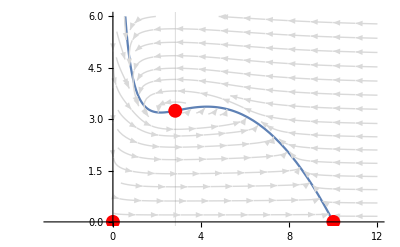

```mathematica
Plot1=Plot[Cstar[[1,1,2]]/.parms,{R,0,12},GridLines->{{{Rstar[[2,1,2]]/.parms,{Red,Thick}}},None},PlotRange->{All,{0,6}} ];Plot2=StreamPlot[{dRdt,dCdt}/.parms,{R,0,12},{C,0,6},StreamStyle->LightGray];
Show[Plot1,Plot2,Graphics[{PointSize[0.025],Red,Point[equil[[All,All,2]]/.parms]}]]
```

```mathematica
With density-independent Immigration
```

```mathematica
Clear["Global`*"]
dRdt=Ι + b R (1-α R) - (a R C)/(1 + a h R)
dCdt= (e a R C)/(1 + a h R) - d C
```

-(a C R)/(1+a h R)+b R (1-R α)+Ι

-C d+(a C e R)/(1+a h R)

```mathematica
(* Solve for isoclines  & Solve for equilibria *)
Rstar=Solve[dCdt==0,R]
Cstar=Solve[dRdt==0,C]

equil=Solve[{dRdt==0,dCdt==0},{R,C}];
%//TableForm
```

{{R→d/(a (e-d h))}}

{{C→-((1+a h R) (-b R+b R^2 α-Ι))/(a R)}}

R→d/(a (e-d h)) | C→(e (a b d e-a b d^2 h-b d^2 α+a^2 e^2 Ι-2 a^2 d e h Ι+a^2 d^2 h^2 Ι))/(a^2 d (e-d h)^2)
R→(b-√b √(b+4 α Ι))/(2 b α) | C→0
R→(b+√b √(b+4 α Ι))/(2 b α) | C→0

```mathematica
parms={b-> 0.8,α-> 0.1,a-> 0.25,e-> 0.1,h-> 1.5, d-> 0.05,Ι-> 0.2};
```

```mathematica
equil/.parms//TableForm
```

R→8. | C→2.96
R→-0.244044 | C→0
R→10.244 | C→0

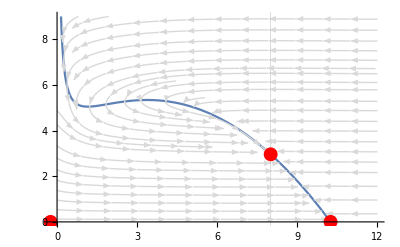

```mathematica
Plot1=Plot[Cstar[[1,1,2]]/.parms,{R,0,12},GridLines->{{{Rstar[[1,1,2]]/.parms,{Red,Thick}}},None},PlotRange->{All,{0,9}} ];Plot2=StreamPlot[{dRdt,dCdt}/.parms,{R,0,12},{C,0,9},StreamStyle->LightGray];
Show[Plot1,Plot2,Graphics[{PointSize[0.025],Red,Point[equil[[All,All,2]]/.parms]}]]
```

```mathematica
With "physical" refuge from predation
```

```mathematica
Clear["Global`*"]
dRdt=b R (1-α R) - (a (R-G) C)/(1 + a h (R-G))
dCdt= (e a (R-G) C)/(1 + a h (R-G)) - d C
```

-(a C (-G+R))/(1+a h (-G+R))+b R (1-R α)

-C d+(a C e (-G+R))/(1+a h (-G+R))

```mathematica
(* Solve for isoclines  & Solve for equilibria *)
Rstar=Solve[dCdt==0,R]
Cstar=Solve[dRdt==0,C]

equil=Solve[{dRdt==0,dCdt==0},{R,C}];
%//TableForm
```

{{R→(d+a e G-a d G h)/(a (e-d h))}}

{{C→(b R (1-a G h+a h R) (-1+R α))/(a (G-R))}}

R→0 | C→0
R→(d+a e G-a d G h)/(a (e-d h)) | C→-(b e (d+a e G-a d G h) (-a e+a d h+d α+a e G α-a d G h α))/(a^2 d (e-d h)^2)
R→1/α | C→0

```mathematica
parms={b-> 0.8,α-> 0.1,a-> 0.25,e-> 0.1,h-> 1.5, d-> 0.05,G-> 0.2};
```

```mathematica
equil/.parms//TableForm
```

R→0 | C→0
R→8.2 | C→2.3616
R→10. | C→0

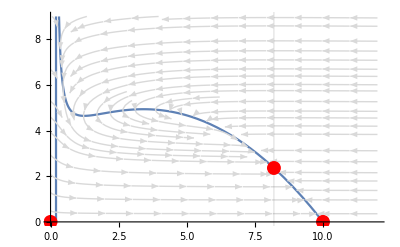

```mathematica
Plot1=Plot[Cstar[[1,1,2]]/.parms,{R,0,12},GridLines->{{{Rstar[[1,1,2]]/.parms,{Red,Thick}}},None},PlotRange->{All,{0,9}} ];Plot2=StreamPlot[{dRdt,dCdt}/.parms,{R,0,12},{C,0,9},StreamStyle->LightGray];
Show[Plot1,Plot2,Graphics[{PointSize[0.025],Red,Point[equil[[All,All,2]]/.parms]}]]
```

```mathematica
The mechanism common to all is that the prey experiences reduced predator - induced mortality at low population sizes.All, in a sense, provide the prey with a "refuge" at low population sizes. With a Type III functional response this refuge is phenomenological in that the predator "switches" to some unmodeled prey.With density - independent immigration, the predator cannot suppress the prey at low population sizes because the prey' s growth rate is dependent more upon immigration (which the predator can' t control) than it is dependent on the number of prey in the population.
```